```mathematica
w[s_]=1/s^2
K[s_,x_]=s(1+w[s])^((q[x]+1)/2)
```

1/s^2

(1+1/s^2)^(1/2 (1+q[x])) s

```mathematica
Simplify[D[K[s,x],s]]
Simplify[D[K[s,x],x]]
Simplify[D[K[s,x],s,s]]
Simplify[D[K[s,x],s,s]-w[s]/s (1+w[s])^((q[x]-3)/2) (w[s] q[x]+1) (q[x]+1)]
Simplify[D[K[s,x],s,x]/(1+w[s])^((q[x]-1)/2)]
Simplify[D[K[s,x],s,x]/(1+w[s])^((q[x]-1)/2)-1/2 q'[x] ((1-q[x] w[s]) Log[1+w[s]]-2 w[s])]
Simplify[D[K[s,x],x,x]/(1+w[s])^((q[x]+1)/2)]
```

((1+1/s^2)^(1/2 (1+q[x])) (s^2-q[x]))/(1+s^2)

1/2 (1+1/s^2)^(1/2 (1+q[x])) s Log[1+1/s^2] q'[x]

((1+1/s^2)^(1/2 (1+q[x])) (1+q[x]) (s^2+q[x]))/(s (1+s^2)^2)

0

((-2+s^2 Log[1+1/s^2]-Log[1+1/s^2] q[x]) q'[x])/(2 s^2)

0

1/4 s Log[1+1/s^2] (Log[1+1/s^2] q'[x]^2+2 q''[x])

```mathematica
det[s_,x_]=D[K[s,x],s,s] D[K[s,x],x,x] -D[K[s,x],s,x]^2
```

-(-((1+1/s^2)^(-1+1/2 (1+q[x])) q'[x])/s^2+1/2 (1+1/s^2)^(1/2 (1+q[x])) Log[1+1/s^2] q'[x]-((1+1/s^2)^(-1+1/2 (1+q[x])) Log[1+1/s^2] (1+q[x]) q'[x])/(2 s^2))^2+(((1+1/s^2)^(-1+1/2 (1+q[x])) (1+q[x]))/s^3+(2 (1+1/s^2)^(-2+1/2 (1+q[x])) (1+q[x]) (-1+1/2 (1+q[x])))/s^5) (1/4 (1+1/s^2)^(1/2 (1+q[x])) s Log[1+1/s^2]^2 q'[x]^2+1/2 (1+1/s^2)^(1/2 (1+q[x])) s Log[1+1/s^2] q''[x])

```mathematica
Simplify[4 det[s,x]/(1+w[s])^(q[x]-1)]
Simplify[4 det[s,x]/(1+w[s])^(q[x]-1)-(w[s] (w[s] q[x]+1)(q[x]+1) Log[1+w[s]] (q'[x]^2 Log[1+w[s]]+2 q''[x])-q'[x]^2 ((1-q[x] w[s]) Log[1+w[s]]-2 w[s])^2)]
b[q_,w_]=2 w (w q +1) (q+1) Log[1+w]
c[q_,w_]=((1-q w) Log[1+w]-2 w)^2-w (w q+1) (q+1) Log[1+w]^2
myDet[s_,x_]=b[q[x],w[s]] q''[x]-c[q[x],w[s]] q'[x]^2
Simplify[4 det[s,x]/(1+w[s])^(q[x]-1)-myDet[s,x]]
```

1/s^4((-4+4 s^2 Log[1+1/s^2]+(s^2-s^4) Log[1+1/s^2]^2+Log[1+1/s^2] (-4+(1+3 s^2) Log[1+1/s^2]) q[x]) q'[x]^2+2 Log[1+1/s^2] (1+q[x]) (s^2+q[x]) q''[x])

0

2 (1+q) w (1+q w) Log[1+w]

-(1+q) w (1+q w) Log[1+w]^2+(-2 w+(1-q w) Log[1+w])^2

-(-(Log[1+1/s^2]^2 (1+q[x]) (1+q[x]/s^2))/s^2+(-2/s^2+Log[1+1/s^2] (1-q[x]/s^2))^2) q'[x]^2+(2 Log[1+1/s^2] (1+q[x]) (1+q[x]/s^2) q''[x])/s^2

0

```mathematica
A[q_,w_]=q c[q,w]/b[q,w]
```

(q (-(1+q) w (1+q w) Log[1+w]^2+(-2 w+(1-q w) Log[1+w])^2))/(2 (1+q) w (1+q w) Log[1+w])

```mathematica
Simplify[A[q,w]]
```

-1/2 q Log[1+w]+(q (2 w+(-1+q w) Log[1+w])^2)/(2 (1+q) w (1+q w) Log[1+w])

```mathematica
Plot3D[A[q,w],{q,0, 10}, {w, 0, 10},AxesLabel->Automatic,PlotRange->Full]
```

-Graphics3D-

```mathematica
FindMaximum[A[q,w],{q,w}]
```

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

{0.627178,{q→4.88476×10^7,w→1.81696}}

```mathematica
Simplify[A[q,w]-q/(q+1) (q (4 w-(w+3) Log[1+w])-(w-1)/w Log[1+w]+4 w/Log[1+w]-4)/(q w+1)/2]
```

0

```mathematica
Simplify[A[q,w]-q/(q+1) ((-q w - 3 q - 1 + 1/w) Log[1+w]+4 w/Log[1+w]+4 (q w -1))/(q w+1)/2]
```

0

```mathematica
Plot3D[q/(q+1) (q (4 w-(w+3) Log[1+w])-(w-1)/w Log[1+w]+4 w/Log[1+w]-4)/(q w+1),{q,0, 10}, {w, 0, 10},AxesLabel->Automatic,PlotRange->Full]
```

-Graphics3D-

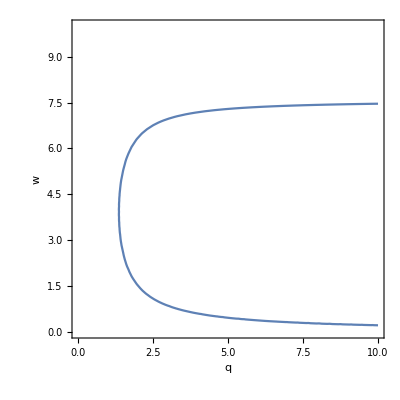

```mathematica
ContourPlot[A[q,w]==1/2,{q,0,10}, {w,0,10},AxesLabel->Automatic]
```

```mathematica
FindMinimum[{q,A[q,w]==1/2},{q,w}]
```

{1.36183,{q→1.36183,w→3.92155}}

```mathematica
A[1.36,4]
```

0.499872